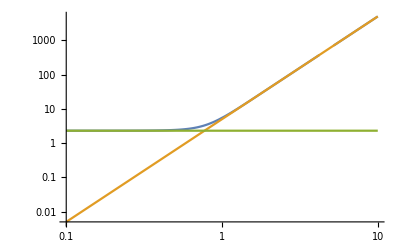

```mathematica
LogLogPlot[{-Log[Exp[5r^3]/Sum[Exp[i r^3],{i,10}]],5r^3,Log[10]},{r,10^-1,10^1}]
```

```mathematica
1/r*%
```

-1/r ⅇ^(-5 r^3) (ⅇ^(r^3)+ⅇ^(2 r^3)+ⅇ^(3 r^3)+ⅇ^(4 r^3)+ⅇ^(5 r^3)+ⅇ^(6 r^3)+ⅇ^(7 r^3)+ⅇ^(8 r^3)+ⅇ^(9 r^3)+ⅇ^(10 r^3)) ((15 ⅇ^(5 r^3) r^2)/(ⅇ^(r^3)+ⅇ^(2 r^3)+ⅇ^(3 r^3)+ⅇ^(4 r^3)+ⅇ^(5 r^3)+ⅇ^(6 r^3)+ⅇ^(7 r^3)+ⅇ^(8 r^3)+ⅇ^(9 r^3)+ⅇ^(10 r^3))-(ⅇ^(5 r^3) (3 ⅇ^(r^3) r^2+6 ⅇ^(2 r^3) r^2+9 ⅇ^(3 r^3) r^2+12 ⅇ^(4 r^3) r^2+15 ⅇ^(5 r^3) r^2+18 ⅇ^(6 r^3) r^2+21 ⅇ^(7 r^3) r^2+24 ⅇ^(8 r^3) r^2+27 ⅇ^(9 r^3) r^2+30 ⅇ^(10 r^3) r^2))/((ⅇ^(r^3)+ⅇ^(2 r^3)+ⅇ^(3 r^3)+ⅇ^(4 r^3)+ⅇ^(5 r^3)+ⅇ^(6 r^3)+ⅇ^(7 r^3)+ⅇ^(8 r^3)+ⅇ^(9 r^3)+ⅇ^(10 r^3))^2))

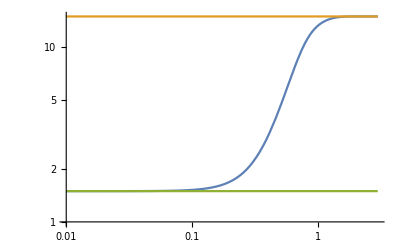

```mathematica
LogLogPlot[{-1/r^2 ⅇ^(-5 r^3) (ⅇ^(r^3)+ⅇ^(2 r^3)+ⅇ^(3 r^3)+ⅇ^(4 r^3)+ⅇ^(5 r^3)+ⅇ^(6 r^3)+ⅇ^(7 r^3)+ⅇ^(8 r^3)+ⅇ^(9 r^3)+ⅇ^(10 r^3)) ((15 ⅇ^(5 r^3) r^2)/(ⅇ^(r^3)+ⅇ^(2 r^3)+ⅇ^(3 r^3)+ⅇ^(4 r^3)+ⅇ^(5 r^3)+ⅇ^(6 r^3)+ⅇ^(7 r^3)+ⅇ^(8 r^3)+ⅇ^(9 r^3)+ⅇ^(10 r^3))-(ⅇ^(5 r^3) (3 ⅇ^(r^3) r^2+6 ⅇ^(2 r^3) r^2+9 ⅇ^(3 r^3) r^2+12 ⅇ^(4 r^3) r^2+15 ⅇ^(5 r^3) r^2+18 ⅇ^(6 r^3) r^2+21 ⅇ^(7 r^3) r^2+24 ⅇ^(8 r^3) r^2+27 ⅇ^(9 r^3) r^2+30 ⅇ^(10 r^3) r^2))/((ⅇ^(r^3)+ⅇ^(2 r^3)+ⅇ^(3 r^3)+ⅇ^(4 r^3)+ⅇ^(5 r^3)+ⅇ^(6 r^3)+ⅇ^(7 r^3)+ⅇ^(8 r^3)+ⅇ^(9 r^3)+ⅇ^(10 r^3))^2)),15,1.5},{r,10^-2,3}]
```

```mathematica
Convergents[300/229]
```

{1,4/3,17/13,38/29,131/100,300/229}

```mathematica
3/4*3000
```

2250

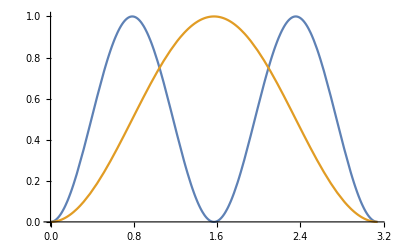

```mathematica
Plot[{Sin[2x]^2,Sin[x]^2},{x,0,Pi}]
```

```mathematica
Sin[2ArcSin[Sqrt[.597+.024]]]^2
```

0.941436

```mathematica
Sin[2ArcSin[Sqrt[.417-.028]]]^2
```

0.950716

```mathematica
Sin[2*0.6154797086703875]^2
```

0.888889

```mathematica
ArcSin[1/Sqrt[3]]/Degree//N
```

35.2644

```mathematica
Sqrt[8.*10^-5]
```

0.00894427

```mathematica
Convergents[N[GoldenRatio,3]]
```

{1,2,3/2,5/3,8/5,13/8,21/13}

```mathematica
Log[10]//N
```

2.30259

```mathematica
?Sum
```

Sum[f,{i,i_max}] evaluates the sum ∑_(i=1)^i_max f. 
Sum[f,{i,i_min,i_max}] starts with i=i_min. 
Sum[f,{i,i_min,i_max,di}] uses steps di. 
Sum[f,{i,{i_1,i_2,…}}] uses successive values i_1, i_2, ….
Sum[f,{i,i_min,i_max},{j,j_min,j_max},…] evaluates the multiple sum ∑_(i=i_min)^i_max ∑_(j=j_min)^j_max …f. 
Sum[f,i] gives the indefinite sum ∑_i f.